# Auditing Protein-Dynamics Models with Structural Nulls

This notebook reconstructs a homology-aware protein-dynamics benchmark from frozen residue-level predictions. It verifies the reported Macro-H result against the original stored results and tests whether the signal disappears under scrambled-data controls.

## Does adding static contact-graph information improve residue-level protein-dynamics prediction beyond an angular-only structural baseline when performance is evaluated across homology-aware ECOD H-groups?

## Data and Provenance

The analysis uses 2,000 frozen held-out residue predictions drawn from 100 proteins, with exactly 20 sampled residues per protein. Proteins are assigned to 59 ECOD H-groups for homology-aware aggregation. No models are retrained in this notebook; it reconstructs statistics from persisted experimental outputs.

```mathematica
SetDirectory[NotebookDirectory[]];

requiredFiles={"sample_residue_data.csv","cohort_selection_manifest.json","results.json","null_results.json"};

If[!And@@(FileExistsQ/@requiredFiles),Print["ERROR: Missing required artifact file(s):"];
Print[Select[requiredFiles,!FileExistsQ[#]&]];
Abort[]];

expectedSHA256="3a42e891ebf54e141544b675ee5c113842bda57cef6212b89942aea4ace04d26";

observedSHA256=IntegerString[FileHash["sample_residue_data.csv","SHA256"],16,64];

provenance=Grid[{{"Artifact","Auditing Protein-Dynamics Models with Structural Nulls"},{"Canonical run","run_20260824T154329Z"},{"Run commit","44945311f38bcdeb7b45be911fc8432bcc275d79"},{"Frozen input","sample_residue_data.csv"},{"Observed SHA256",observedSHA256},{"SHA256 matches frozen input",observedSHA256===expectedSHA256},{"Residues",2000},{"Proteins",100},{"ECOD H-groups",59},{"Wolfram version",$Version},{"Retraining performed",False}},Frame->All,Alignment->Left,Spacings->{2,1}];

provenance
raw=Import["sample_residue_data.csv","CSV"];
header=First[raw];
rows=AssociationThread[header,#]&/@Rest[raw];

{"Residue rows"->Length[rows],"Proteins"->Length@DeleteDuplicates[Lookup[rows,"protein_id"]],"Fold counts"->Counts[Lookup[rows,"fold_id"]]}
```

Artifact | Auditing Protein-Dynamics Models with Structural Nulls
Canonical run | run_20260824T154329Z
Run commit | 44945311f38bcdeb7b45be911fc8432bcc275d79
Frozen input | sample_residue_data.csv
Observed SHA256 | 3a42e891ebf54e141544b675ee5c113842bda57cef6212b89942aea4ace04d26
SHA256 matches frozen input | True
Residues | 2000
Proteins | 100
ECOD H-groups | 59
Wolfram version | 15.0.1 for Linux x86 (64-bit) (July 2, 2026)
Retraining performed | False

{Residue rows→2000,Proteins→100,Fold counts→<|0→400,3→400,2→400,4→400,1→400|>}

## Per-Protein Reconstruction

For each protein, Spearman correlation is computed across its 20 held-out residue predictions. This produces one correlation score per protein for each model arm before any homology-group aggregation.

```mathematica
byProtein=GroupBy[rows,#["protein_id"]&];

proteinMetrics=Map[Function[pRows,<|"A"->SpearmanRho[Lookup[pRows,"target_y"],Lookup[pRows,"pred_A"]],"C"->SpearmanRho[Lookup[pRows,"target_y"],Lookup[pRows,"pred_C"]],"A_attr_control"->SpearmanRho[Lookup[pRows,"target_y"],Lookup[pRows,"pred_A_attr_control"]],"plddt"->SpearmanRho[Lookup[pRows,"target_y"],Lookup[pRows,"pred_plddt"]]|>],byProtein];

macroProtein=AssociationMap[Mean[Lookup[Values[proteinMetrics],#]]&,{"A","C","A_attr_control","plddt"}];

{"Proteins"->Length[proteinMetrics],"Residues per protein"->Counts[Length/@Values[byProtein]],"Macro-protein"->macroProtein,"C - A"->(macroProtein["C"]-macroProtein["A"])}
```

{Proteins→100,Residues per protein→<|20→100|>,Macro-protein→<|A→0.103368,C→0.330797,A_attr_control→0.0718045,plddt→0.357112|>,C - A→0.227429}

## Homology-Aware Macro-H Reconstruction

To avoid overweighting proteins from the same structural family, protein-level scores are grouped by ECOD H-group. Each H-group contributes one mean score, and the final Macro-H statistic is the equal-weight mean across 59 groups.

```mathematica
cohort=Import["cohort_selection_manifest.json","RawJSON"];

proteinToHGroup=Association@Flatten[Function[g,Thread[g["protein_ids"]->g["h_group"]]]/@cohort["h_groups"]];

hGroupProteins=GroupBy[Keys[proteinMetrics],proteinToHGroup[#]&];

hGroupMetrics=Map[Function[pids,AssociationMap[Function[arm,Mean[(proteinMetrics[#][arm]&)/@pids]],{"A","C","A_attr_control","plddt"}]],hGroupProteins];

macroH=AssociationMap[Function[arm,Mean[(#[arm]&)/@Values[hGroupMetrics]]],{"A","C","A_attr_control","plddt"}];

{"H-groups"->Length[hGroupMetrics],"Macro-H"->macroH,"C - A"->(macroH["C"]-macroH["A"])}
```

{H-groups→59,Macro-H→<|A→0.114298,C→0.336625,A_attr_control→0.0872818,plddt→0.345523|>,C - A→0.222327}

## Authority Validation

The reconstructed Macro-H values are compared against the persisted Phase-4A results. Agreement to machine precision confirms that the Wolfram reconstruction reproduces the stored benchmark statistic without retraining any model.

```mathematica
authority=Import["results.json","RawJSON"];

authorityMacro=AssociationMap[authority["macros"][#]["macro_hgroup_spearman"]&,{"A","C","A_attr_control","plddt"}];

differences=AssociationMap[macroH[#]-authorityMacro[#]&,Keys[authorityMacro]];

{"Reconstruction"->macroH,"Stored authority"->authorityMacro,"Max absolute difference"->Max[Abs[Values[differences]]],"PASS"->(Max[Abs[Values[differences]]]<10^-12)}
```

{Reconstruction→<|A→0.114298,C→0.336625,A_attr_control→0.0872818,plddt→0.345523|>,Stored authority→<|A→0.114298,C→0.336625,A_attr_control→0.0872818,plddt→0.345523|>,Max absolute difference→1.11022×10^-16,PASS→True}

## Structural Null Audit

Structural null controls deliberately break the relationship between the biological target and the model predictions. If the benchmark signal is meaningful, these scrambled controls should collapse toward zero rather than preserve the real-data performance.

```mathematica
nulls=Import["null_results.json","RawJSON"];

nullSummary=AssociationMap[nulls["macros"][#]["macro_hgroup_spearman"]&,{"A_null_global","A_null_within","A_attr_control_null_global","A_attr_control_null_within","C_null_global","C_null_within"}];

{"Null scores"->nullSummary,"All |rho| < 0.1"->AllTrue[Values[nullSummary],Abs[#]<0.1&]}
```

{Null scores→<|A_null_global→0.0088314,A_null_within→-0.00482987,A_attr_control_null_global→0.0120046,A_attr_control_null_within→-0.0161208,C_null_global→-0.0703581,C_null_within→-0.00581114|>,All |rho| < 0.1→True}

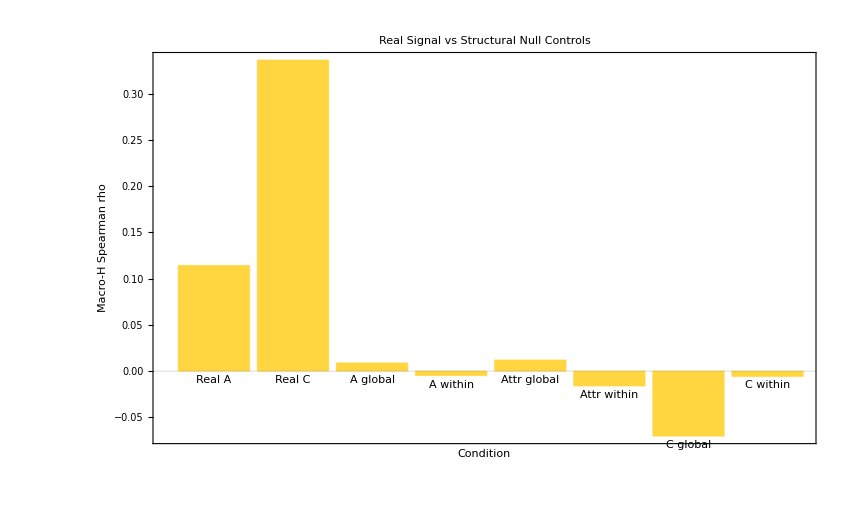

```mathematica
plotData=<|"Real A"->macroH["A"],"Real C"->macroH["C"],"A global"->nullSummary["A_null_global"],"A within"->nullSummary["A_null_within"],"Attr global"->nullSummary["A_attr_control_null_global"],"Attr within"->nullSummary["A_attr_control_null_within"],"C global"->nullSummary["C_null_global"],"C within"->nullSummary["C_null_within"]|>;

nullAuditFigure=BarChart[Values[plotData],ChartLabels->Placed[Keys[plotData],Below],Frame->True,Axes->False,FrameLabel->{"Condition","Macro-H Spearman rho"},PlotLabel->"Real Signal vs Structural Null Controls",GridLines->{None,{0}},ImageSize->850];

nullAuditFigure
```

## Results and Interpretation

The graph-enhanced model C achieves a Macro-H Spearman correlation of 0.3366 compared with 0.1143 for the angular-only model A, an improvement of +0.2223. The reconstructed values match the persisted Phase-4A results to machine precision. All six structural null controls remain within |rho| < 0.1, indicating that the observed performance does not persist when the target-prediction relationship is deliberately disrupted.

These results support the conclusion that the graph-enhanced structural representation captures predictive information beyond the angular-only baseline under homology-aware evaluation. They do not establish superiority over every alternative representation: pLDDT reaches a similar Macro-H score, and this notebook reconstructs frozen predictions rather than retraining the underlying models.

## Reproducibility

This notebook operates only on persisted experimental outputs. No model training is performed. The analysis begins from the frozen residue-level prediction table, reconstructs per-protein Spearman correlations, aggregates them equally across 59 ECOD H-groups, validates the resulting Macro-H statistics against stored authority, and audits six structural null controls.

```mathematica
{"Rows"->Length[rows],"Proteins"->Length[proteinMetrics],"H-groups"->Length[hGroupMetrics],"C - A"->(macroH["C"]-macroH["A"]),"Authority PASS"->(Max[Abs[Values[differences]]]<10^-12),"Null PASS"->AllTrue[Values[nullSummary],Abs[#]<0.1&]}
```

{Rows→2000,Proteins→100,H-groups→59,C - A→0.222327,Authority PASS→True,Null PASS→True}

## H-Group Performance Landscape

Each point represents one ECOD H-group. Points above the diagonal indicate H-groups where the graph-enhanced model C outperforms the angular-only model A.

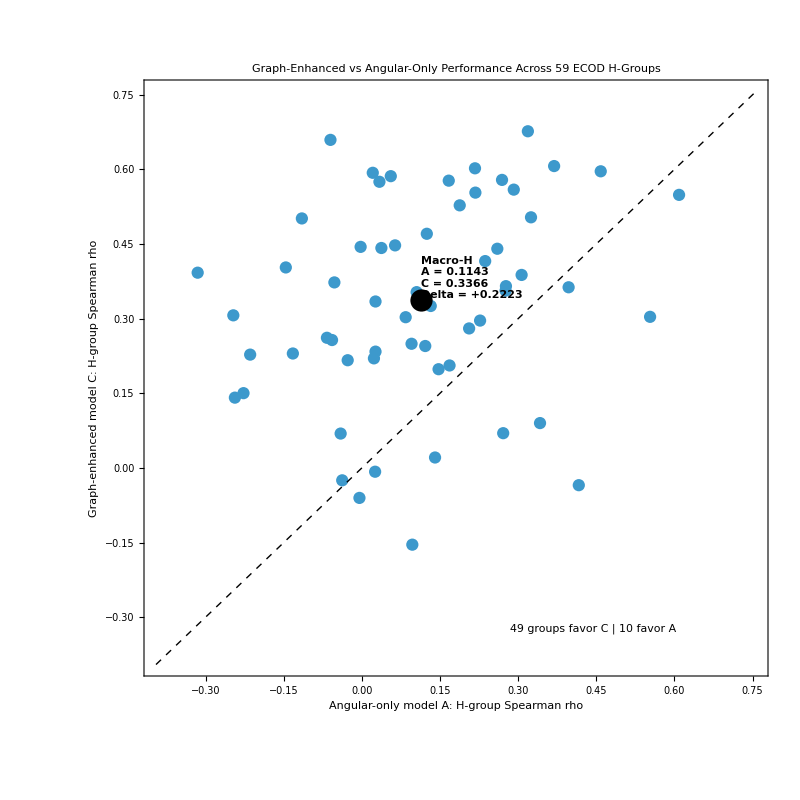

```mathematica
scatterPoints=({#["A"],#["C"]}&)/@Values[hGroupMetrics];

deltas=#[[2]]-#[[1]]&/@scatterPoints;

nCFavor=Count[deltas,x_/;x>0];
nAFavor=Count[deltas,x_/;x<0];

rangeMin=Min[Flatten[scatterPoints]]-0.08;
rangeMax=Max[Flatten[scatterPoints]]+0.08;

hGroupScatter=ListPlot[scatterPoints,Frame->True,Axes->False,AspectRatio->1,ImageSize->800,FrameLabel->{"Angular-only model A: H-group Spearman rho","Graph-enhanced model C: H-group Spearman rho"},PlotRange->{{rangeMin,rangeMax},{rangeMin,rangeMax}},PlotLabel->"Graph-Enhanced vs Angular-Only Performance Across 59 ECOD H-Groups",Epilog->{Dashed,Line[{{rangeMin,rangeMin},{rangeMax,rangeMax}}],PointSize[0.02],Point[{macroH["A"],macroH["C"]}],Text[Style["Macro-H\nA = 0.1143\nC = 0.3366\nDelta = +0.2223",11,Bold],{macroH["A"],macroH["C"]},{-1.3,-1.2}],Text[Style[ToString[nCFavor]<>" groups favor C | "<>ToString[nAFavor]<>" favor A",11],Scaled[{0.72,0.08}]]}];

hGroupScatter
```

## Uncertainty of the Primary Contrast

```mathematica
boot=authority["bootstrap_C_minus_A"];
ci=boot["ci95"];

uncertaintyPanel=Panel[Grid[{{"Primary contrast","C - A"},{"Observed delta",NumberForm[boot["delta"],{6,4}]},{"95% bootstrap CI",Row[{"[",NumberForm[ci[[1]],{6,4}],", ",NumberForm[ci[[2]],{6,4}],"]"}]},{"Bootstrap replicates",boot["n_boot"]},{"ECOD H-groups",boot["n_h_groups"]},{"Interval excludes zero",Not[ci[[1]]<=0<=ci[[2]]]}},Frame->All,Alignment->Left,Spacings->{2,1}]];

uncertaintyPanel
```

Primary contrast | C - A
Observed delta | 0.2223
95% bootstrap CI | [0.1626, 0.2836]
Bootstrap replicates | 2000
ECOD H-groups | 59
Interval excludes zero | True

The primary Macro-H contrast is +0.2223, with a 95% H-group bootstrap confidence interval of [+0.1626, +0.2836]. Because the interval remains above zero, the improvement of model C over model A is supported across the homology-aware evaluation rather than being driven solely by the point estimate.

## Interactive H-Group Explorer

Select an ECOD H-group to inspect its constituent proteins, compare model A and model C, and locate that group within the full performance landscape.

```mathematica
groupKeys=Sort[Keys[hGroupMetrics]];

Manipulate[With[{m=hGroupMetrics[hg],pids=hGroupProteins[hg]},Column[{Panel[Grid[{{"ECOD H-group",hg},{"Proteins",Length[pids]},{"Model A",NumberForm[m["A"],{5,3}]},{"Model C",NumberForm[m["C"],{5,3}]},{"C - A",NumberForm[m["C"]-m["A"],{5,3}]},{"Favors",If[m["C"]>m["A"],"Graph-enhanced C","Angular-only A"]}},Frame->All,Alignment->Left,Spacings->{2,1}]],Dataset[(<|"Protein"->#,"A"->proteinMetrics[#]["A"],"C"->proteinMetrics[#]["C"],"C - A"->proteinMetrics[#]["C"]-proteinMetrics[#]["A"]|>)&/@pids],Show[hGroupScatter,Graphics[{Directive[Red,PointSize[0.03]],Point[{m["A"],m["C"]}],Text[Style["Selected: "<>ToString[hg],12,Bold,Red],{m["A"],m["C"]},{0,-1.5}]}],ImageSize->650]},Spacings->2]],{{hg,First[groupKeys],"ECOD H-group"},groupKeys,ControlType->PopupMenu}]
```

## Conclusion

Across 59 ECOD H-groups, the graph-enhanced model C achieves a Macro-H Spearman correlation of 0.3366 compared with 0.1143 for the angular-only model A, yielding a primary contrast of +0.2223. The 95% H-group bootstrap confidence interval [+0.1626, +0.2836] remains above zero. The Wolfram reconstruction matches the persisted Phase-4A authority to machine precision, and all six structural null controls remain within |rho| < 0.1. Together, these results support a reproducible homology-aware improvement of C over A without implying superiority over every alternative baseline.